```mathematica
muB = 6.71711388`20*10^(5);
p=0.63496`20;
V0 = 3.326`20;
xr = 9.9747`20;
cB =1.0`20;
Bp=18.92`20*10^(-8);
hbar=7.63823302`20;mass=723.453025853;
RLOffset=0.5`20;
V[x_]:=p*V0*(1-1/(1+(x/xr)^2))-cB*muB*Bp*x+RLOffset;
NSolve[V[x]==0,x]
LH=Solve[V'[x]==0,x];
xmin=x/.LH[[3]];Vmin=V[xmin];
omega=Sqrt[D[V[x],{x,2}]/.{x->xmin}]/Sqrt[mass];xmin
omega
```

{{x→15.8283011952523236},{x→2.36172588612038661+4.37637676583649931 ⅈ},{x→2.36172588612038661-4.37637676583649931 ⅈ}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

4.078169689720613228

0.00428935

```mathematica
omega
```

0.00431708

```mathematica
Series[V[x],{x,xmin,5}]
```

0.282557589997785428+0.00651488984413073855 (x-4.108180518208179183)^2-0.00155546055435230574 (x-4.108180518208179183)^3+0.00005383895698296731 (x-4.108180518208179183)^4+9.5650352388889231×10^-6 (x-4.108180518208179183)^5+O[x-4.108180518208179183]^6

```mathematica
Sqrt[0.00651488984413073854747597681493683920199006897425657441*2/mass]
```

0.00424388

```mathematica
Series[V[x],{x,xmin,2}]
```

0.282557589997785428+0.00651488984413073855 (x-4.108180518208179183)^2+O[x-4.108180518208179183]^3

```mathematica
Sqrt[D[V[x],{x,2}]/.{x->xmin}]/Sqrt[mass]
```

0.00424388

```mathematica
Sqrt[2*((V[xmin]+0.014673339226547963))*mass]/hbar
```

2.72241

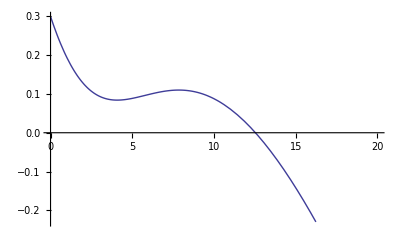

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
Plot[V[x],{x,0,20},PlotRange->{-0.23, 0.3}]
```

```mathematica
e
```

```mathematica
xmin
```

4.078169689720613228

```mathematica
N[V[-7],20]
```

1.785214895972146993

```mathematica
Found=-0.0017058918;
```

```mathematica
DE=Found-Vmin;
```

```mathematica
AA=DE/(hbar*2*Pi)*10^6
```

305.743

```mathematica
1-AA/316.3
```

0.0333773

```mathematica
Vmin
```

-0.016379231026547962

```mathematica
DE
```

0.0146733

```mathematica
xmin
```

4.095753443173048599

```mathematica
LH=Solve[V'[x]==0,x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→-5.958937701101649443-16.53718878196092229 ⅈ},{x→-5.958937701101649443+16.53718878196092229 ⅈ},{x→4.095753443173048599},{x→7.822121959030250288}}

```mathematica
V[xmin]
```

0.283620768973452038

```mathematica
0.28362076897345203790107013027449139198`18.61806273297653/hbar
```

0.037131725129466139

1.54674

```mathematica
+0.0143798664/(hbar*2*Pi)*10^6
```

299.628